```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,200,300,400,500,600};
chi0data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi0.dat"]],{i,1,Length[mub]}];
chi1data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi1.dat"]],{i,1,Length[mub]}];
chi2data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi2.dat"]],{i,1,Length[mub]}];
chi3data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi3.dat"]],{i,1,Length[mub]}];
chi4data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi4.dat"]],{i,1,Length[mub]}];
T=Table[10+2i,{i,1,125}];
poT4data=Table[Transpose[{T,chi0data[[i]]/T^4}],{i,1,Length[mub]}];
c1data=Table[Transpose[{T,chi1data[[i]]}],{i,1,Length[mub]}];
c2data=Table[Transpose[{T,T^2 chi2data[[i]]^-1}],{i,1,Length[mub]}];
```

```mathematica
(*c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
c5=T^11(-15(1/chi2)^7(chi3)^3-(1/chi2)^5 chi5+10(1/chi2)^6 chi3 chi4);
c6=T^14(105(1/chi2)^9 chi3^4-105(1/chi2)^8 chi3^2 chi4+10(1/chi2)^7 chi4^2+15(1/chi2)^7 chi3 chi5-(1/chi2)^6 chi6);*)
```

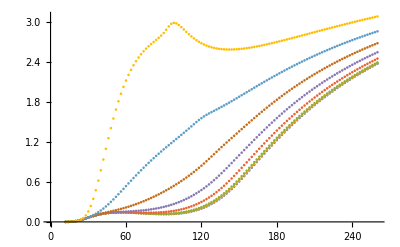

```mathematica
ListPlot[poT4data]
```

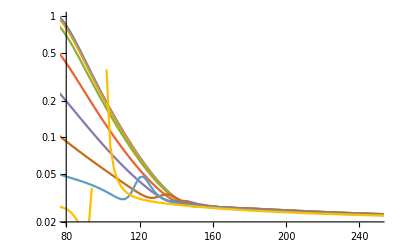

```mathematica
ListLinePlot[c2data,PlotRange->{{80,250},{0.02,1.}},ScalingFunctions->"Log"]
```